```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/中化II/figures"];
```

```mathematica
<<MaTeX`
TimesNewRoman[string_]:=Style[string,"Times New Roman",12,Black];
GraphFormatize[object_,otheroption___]:=Show[object,Frame->True,Axes->False,FrameTicksStyle->Directive[12,Black,"Times New Roman"],FrameStyle->Thickness[0.003],PlotStyle->Black,otheroption];
```

```mathematica
KClDataList={{{1/16,2500,2000,1725.50},{1/16,2500,3000,2611.00},{1/16,2500,4000,3478.00}},{{1/8,2500,4000,2161.70},{1/8,2500,5000,2652.50}},{{1/4,2500,5000,1413.40},{1/4,2500,6000,1700.70},{1/4,2500,7000,1952.50}},{{1/2,2500,7000,1127.40},{1/2,2500,8000,1290.80},{1/2,2500,9000,1410.30}},{{1,2500,2500,215.00},{1,2500,5000,431.21},{1,2500,10000,861.00}}};
```

```mathematica
TableForm[Flatten[{{{1/16,2500,2000,1725.50},{1/16,2500,3000,2611.00},{1/16,2500,4000,3478.00}},{{1/8,2500,4000,2161.70},{1/8,2500,5000,2652.50}},{{1/4,2500,5000,1413.40},{1/4,2500,6000,1700.70},{1/4,2500,7000,1952.50}},{{1/2,2500,7000,1127.40},{1/2,2500,8000,1290.80},{1/2,2500,9000,1410.30}},{{1,2500,2500,215.00},{1,2500,5000,431.21},{1,2500,10000,861.00}}},1]]//TeXForm
```

```mathematica
({1/16,1/8,1/4,1/2,1}*0.02)~SetPrecision~4
```

{0.00125,0.0025,0.005,0.01,0.02}

```mathematica
enhancedkcldata=Mean/@(Map[{Sqrt[#[[1]]*0.02],59.52630250000001/(#[[2]]/#[[3]]*#[[4]])/#[[1]]/0.02/1000}&,#]&/@KClDataList)
```

{{0.0353553,0.0219575},{0.05,0.0177884},{0.0707107,0.0169065},{0.1,0.014912},{0.141421,0.013825}}

```mathematica
0.2765/(0.232251*(0.1414213562373095)^2*1000)
```

0.0595261

```mathematica
0.2765*(215+431.21/2+861.00/4)/3
```

59.5263

```mathematica
0.232251*(0.1414213562373095)^2
```

0.00464502

```mathematica
kclline=LinearModelFit[enhancedkcldata[[2;;5]],{1,x},x]
```

FittedModel[0.0199178-0.0448434 x]

```mathematica
kclline//Normal
```

0.0199178-0.0448434 x

```mathematica
Export["kcl.eps",GraphFormatize@Show[ListPlot[enhancedkcldata,PlotStyle->Black,FrameLabel->MaTeX/@{"\sqrt{c}/\mathrm{M^{-1/2}}","\Lambda_m/(S \cdot m^2 \cdot mol^{-1})"}],Plot[kclline//Normal,{x,0,0.15},PlotStyle->Black]]]
```

kcl.eps

```mathematica
SDSdatalist={{{0.005,2500,2500,2124.60},{0.005,2500,3500,2975.80},{0.005,2500,4500,3836.90}},{{0.007,2500,2500,1655.50},{0.007,2500,3500,2307.40},{0.007,2500,5500,3701.00}},{{0.009,2500,2500,1413.13},{0.009,2500,3500,1970.73},{0.009,2500,4500,2503.75}},{{0.010,2500,3000,1541.45},{0.010,2500,4000,2060.05},{0.010,2500,5000,2560.30}},{{0.013,2500,3000,1325.00},{0.013,2500,3000,1309.80},{0.013,2500,4000,1766.50},{0.013,2500,5000,2177.50}},{{0.015,2500,5000,2020.00},{0.015,2500,6000,2400.20},{0.015,2500,8000,3217.40}},{{0.0075,2500,2500,1624.30},{0.0075,2500,3500,2259.30},{0.0075,2500,4500,2910.80}},{{0.0080,2500,2500,1565.00},{0.0080,2500,3500,2259.30},{0.0080,2500,4500,2762.00}},{{0.0085,2500,2500,1506.20},{0.0085,2500,3500,2098.00},{0.0085,2500,4500,2710.25}}};
```

```mathematica
Sort[Flatten[SDSdatalist,1]]//TableForm//TeXForm
```

\begin{array}{cccc}
 0.005 & 2500 & 2500 & 2124.6 \\
 0.005 & 2500 & 3500 & 2975.8 \\
 0.005 & 2500 & 4500 & 3836.9 \\
 0.007 & 2500 & 2500 & 1655.5 \\
 0.007 & 2500 & 3500 & 2307.4 \\
 0.007 & 2500 & 5500 & 3701. \\
 0.0075 & 2500 & 2500 & 1624.3 \\
 0.0075 & 2500 & 3500 & 2259.3 \\
 0.0075 & 2500 & 4500 & 2910.8 \\
 0.008 & 2500 & 2500 & 1565. \\
 0.008 & 2500 & 3500 & 2259.3 \\
 0.008 & 2500 & 4500 & 2762. \\
 0.0085 & 2500 & 2500 & 1506.2 \\
 0.0085 & 2500 & 3500 & 2098. \\
 0.0085 & 2500 & 4500 & 2710.25 \\
 0.009 & 2500 & 2500 & 1413.13 \\
 0.009 & 2500 & 3500 & 1970.73 \\
 0.009 & 2500 & 4500 & 2503.75 \\
 0.01 & 2500 & 3000 & 1541.45 \\
 0.01 & 2500 & 4000 & 2060.05 \\
 0.01 & 2500 & 5000 & 2560.3 \\
 0.013 & 2500 & 3000 & 1309.8 \\
 0.013 & 2500 & 3000 & 1325. \\
 0.013 & 2500 & 4000 & 1766.5 \\
 0.013 & 2500 & 5000 & 2177.5 \\
 0.015 & 2500 & 5000 & 2020. \\
 0.015 & 2500 & 6000 & 2400.2 \\
 0.015 & 2500 & 8000 & 3217.4 \\
\end{array}

```mathematica
enhancedSDS=Sort[Mean/@(Map[{Sqrt[#[[1]]],59.52630250000001/1000/(#[[2]]/#[[3]]*#[[4]])/#[[1]]}&,#]&/@SDSdatalist)];
```

```mathematica
enhancedSDS
```

```mathematica
SDS1line1=LinearModelFit[enhancedSDS[[1;;4]],{1,x},x];
SDS1line2=LinearModelFit[enhancedSDS[[5;;9]],{1,x},x];
```

```mathematica
Solve[Normal[SDS1line1]==Normal[SDS1line2],x]
```

{{x→0.0875198}}

```mathematica
0.08751983295293819^2
```

0.00765972

```mathematica
Solve[Normal[SDS2line1]==Normal[SDS2line2],x]
```

{{x→0.00980442}}

```mathematica
Export["CMC1.eps",GraphFormatize@Show[ListPlot[enhancedSDS,PlotStyle->Black,FrameLabel->MaTeX/@{"\sqrt{c}/\mathrm{M^{-1/2}}","\Lambda_m/(S \cdot m^2 \cdot mol^{-1})"}],Plot[{Normal[SDS1line1],Normal[SDS1line2]},{x,0,0.13},PlotLegends->TimesNewRoman/@{"dilu.","conc."},PlotStyle->{{Black},{Black,Dotted}}]]]
```

OptionValue::nodef: Unknown option PlotStyle for Graphics.

CMC1.eps

```mathematica
enhancedSDS2=Sort[Mean/@(Map[{#[[1]],59.52630250000001/(#[[2]]/#[[3]]*#[[4]])}&,#]&/@SDSdatalist)]
```

{{0.005,0.0279827},{0.007,0.0358194},{0.0075,0.0367813},{0.008,0.0379052},{0.0085,0.0395923},{0.009,0.0424019},{0.01,0.0463576},{0.013,0.0542591},{0.015,0.0592209}}

```mathematica
SDS2line1=LinearModelFit[enhancedSDS2[[1;;4]],{1,x},x];
SDS2line2=LinearModelFit[enhancedSDS2[[5;;9]],{1,x},x];
```

```mathematica
Export["CMC2.eps",GraphFormatize@Show[ListPlot[enhancedSDS2,PlotStyle->Black,FrameLabel->MaTeX/@{"c/\mathrm{M}","\Lambda/(S \cdot m^{-1})"}],Plot[{Normal[SDS2line1],Normal[SDS2line2]},{x,0,0.13},PlotLegends->TimesNewRoman/@{"dilu.","conc."},PlotStyle->{{Black},{Black,Dotted}}]]]
```

OptionValue::nodef: Unknown option PlotStyle for Graphics.

CMC2.eps

```mathematica
Solve[{I1 R1 + (I1-i) R2 ==U,I2 Rx + (I2+i)R3==U,I1 R1 + i r -I2 Rx==0},{I1,I2,Rx}]
```

{{I1→(i R2+U)/(R1+R2),I2→(-i r R1-i r R2-i R1 R2-i R1 R3-i R2 R3+R2 U)/((R1+R2) R3),Rx→-(R3 (i r R1+i r R2+i R1 R2+R1 U))/(i r R1+i r R2+i R1 R2+i R1 R3+i R2 R3-R2 U)}}

```mathematica
-(R3 (i r R1+i r R2+i R1 R2+R1 U))/(i r R1+i r R2+i R1 R2+i R1 R3+i R2 R3-R2 U)/.i->0
```

(R1 R3)/R2

```mathematica
DSolve[U0 Sin[w t]-u[t] == c R D[u[t],t],u[t],t]
```

{{u[t]→ⅇ^(-t/(c R)) C[1]-(U0 (c R w Cos[t w]-Sin[t w]))/(1+c^2 R^2 w^2)}}

```mathematica
WheatstoneSolve=DSolve[{I1[t] R1 + (I1[t]-i[t]) R2 ==U0 Sin[w t],I2[t] Rx + (I2[t]+i[t])R3==U0 Sin[w t]-u[t],(I1[t]-i[t]) R2 - i[t] r -(I2[t]+i[t]) R3==0}/.{I2[t]->c D[u[t],t]},{I1[t],u[t],i[t]},t]
```

{{i[t]→((c R1+c R2) R3 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^2 (ⅇ^(-((r R1+r R2+R1 R2+R1 R3+R2 R3) t)/(c (r R1 R3+r R2 R3+R1 R2 R3+r R1 Rx+r R2 Rx+R1 R2 Rx+R1 R3 Rx+R2 R3 Rx))) C[1]-((r (R1+R2)+R1 (R2+R3)) (R2 R3 (1+c Rx)+r (R1+R2) (1+c (R3+Rx))+R1 (R2+R3+c R3 Rx+c R2 (R3+Rx)))^3 U0 (c (R1 R3 Rx+R2 R3 Rx+R1 R2 (R3+Rx)+r (R1+R2) (R3+Rx)) w Cos[t w]-(r (R1+R2)+R2 R3+R1 (R2+R3)) Sin[t w]))/(c^3 (R1 R3 Rx+R2 R3 Rx+R1 R2 (R3+Rx)+r (R1+R2) (R3+Rx))^3 (R1 R3 (-ⅈ+c Rx w)+R2 R3 (-ⅈ+c Rx w)+R1 R2 (-ⅈ+c (R3+Rx) w)+r (R1+R2) (-ⅈ+c (R3+Rx) w)) (R1 R3 (ⅈ+c Rx w)+R2 R3 (ⅈ+c Rx w)+R1 R2 (ⅈ+c (R3+Rx) w)+r (R1+R2) (ⅈ+c (R3+Rx) w)))))/((r R1+r R2+R1 R2+R1 R3+c r R1 R3+R2 R3+c r R2 R3+c R1 R2 R3+c r R1 Rx+c r R2 Rx+c R1 R2 Rx+c R1 R3 Rx+c R2 R3 Rx) (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^2)-((r R1+r R2+R1 R2+R1 R3+c r R1 R3+R2 R3+c r R2 R3+c R1 R2 R3+c r R1 Rx+c r R2 Rx+c R1 R2 Rx+c R1 R3 Rx+c R2 R3 Rx) (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^5 (((c R1+c R2) R3 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^2 ((c R2 R3 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^2 (r R1 U0 Sin[t w]+r R2 U0 Sin[t w]+R1 R2 U0 Sin[t w]+R1 R3 U0 Sin[t w]))/((r R1+r R2+R1 R2+R1 R3+c r R1 R3+R2 R3+c r R2 R3+c R1 R2 R3+c r R1 Rx+c r R2 Rx+c R1 R2 Rx+c R1 R3 Rx+c R2 R3 Rx)^2 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^2)-((-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^3 (r U0 Sin[t w]+R2 U0 Sin[t w]+R3 U0 Sin[t w]+c r R3 U0 Sin[t w]+c r Rx U0 Sin[t w]+c R2 Rx U0 Sin[t w]+c R3 Rx U0 Sin[t w]))/((r R1+r R2+R1 R2+R1 R3+c r R1 R3+R2 R3+c r R2 R3+c R1 R2 R3+c r R1 Rx+c r R2 Rx+c R1 R2 Rx+c R1 R3 Rx+c R2 R3 Rx) (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^3)))/((r R1+r R2+R1 R2+R1 R3+c r R1 R3+R2 R3+c r R2 R3+c R1 R2 R3+c r R1 Rx+c r R2 Rx+c R1 R2 Rx+c R1 R3 Rx+c R2 R3 Rx) (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^2)-((-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^3 ((c R2 R3 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^2 (R2 U0 Sin[t w]-c R1 R3 U0 Sin[t w]+c R2 Rx U0 Sin[t w]))/((r R1+r R2+R1 R2+R1 R3+c r R1 R3+R2 R3+c r R2 R3+c R1 R2 R3+c r R1 Rx+c r R2 Rx+c R1 R2 Rx+c R1 R3 Rx+c R2 R3 Rx)^2 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^2)-((c R1+c R2) R3 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^2 (r U0 Sin[t w]+R2 U0 Sin[t w]+R3 U0 Sin[t w]+c r R3 U0 Sin[t w]+c r Rx U0 Sin[t w]+c R2 Rx U0 Sin[t w]+c R3 Rx U0 Sin[t w]))/((r R1+r R2+R1 R2+R1 R3+c r R1 R3+R2 R3+c r R2 R3+c R1 R2 R3+c r R1 Rx+c r R2 Rx+c R1 R2 Rx+c R1 R3 Rx+c R2 R3 Rx)^2 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^2)))/(-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^3))/(c R2 R3 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^5),I1[t]→(c R2 R3 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^2 (ⅇ^(-((r R1+r R2+R1 R2+R1 R3+R2 R3) t)/(c (r R1 R3+r R2 R3+R1 R2 R3+r R1 Rx+r R2 Rx+R1 R2 Rx+R1 R3 Rx+R2 R3 Rx))) C[1]-((r (R1+R2)+R1 (R2+R3)) (R2 R3 (1+c Rx)+r (R1+R2) (1+c (R3+Rx))+R1 (R2+R3+c R3 Rx+c R2 (R3+Rx)))^3 U0 (c (R1 R3 Rx+R2 R3 Rx+R1 R2 (R3+Rx)+r (R1+R2) (R3+Rx)) w Cos[t w]-(r (R1+R2)+R2 R3+R1 (R2+R3)) Sin[t w]))/(c^3 (R1 R3 Rx+R2 R3 Rx+R1 R2 (R3+Rx)+r (R1+R2) (R3+Rx))^3 (R1 R3 (-ⅈ+c Rx w)+R2 R3 (-ⅈ+c Rx w)+R1 R2 (-ⅈ+c (R3+Rx) w)+r (R1+R2) (-ⅈ+c (R3+Rx) w)) (R1 R3 (ⅈ+c Rx w)+R2 R3 (ⅈ+c Rx w)+R1 R2 (ⅈ+c (R3+Rx) w)+r (R1+R2) (ⅈ+c (R3+Rx) w)))))/((r R1+r R2+R1 R2+R1 R3+c r R1 R3+R2 R3+c r R2 R3+c R1 R2 R3+c r R1 Rx+c r R2 Rx+c R1 R2 Rx+c R1 R3 Rx+c R2 R3 Rx) (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^2)-((-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^3 ((c R2 R3 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^2 (r R1 U0 Sin[t w]+r R2 U0 Sin[t w]+R1 R2 U0 Sin[t w]+R1 R3 U0 Sin[t w]))/((r R1+r R2+R1 R2+R1 R3+c r R1 R3+R2 R3+c r R2 R3+c R1 R2 R3+c r R1 Rx+c r R2 Rx+c R1 R2 Rx+c R1 R3 Rx+c R2 R3 Rx)^2 (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^2)-((-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^3 (r U0 Sin[t w]+R2 U0 Sin[t w]+R3 U0 Sin[t w]+c r R3 U0 Sin[t w]+c r Rx U0 Sin[t w]+c R2 Rx U0 Sin[t w]+c R3 Rx U0 Sin[t w]))/((r R1+r R2+R1 R2+R1 R3+c r R1 R3+R2 R3+c r R2 R3+c R1 R2 R3+c r R1 Rx+c r R2 Rx+c R1 R2 Rx+c R1 R3 Rx+c R2 R3 Rx) (-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^3)))/(-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^3,u[t]→((-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (c R3+c Rx))^3 (ⅇ^(-((r R1+r R2+R1 R2+R1 R3+R2 R3) t)/(c (r R1 R3+r R2 R3+R1 R2 R3+r R1 Rx+r R2 Rx+R1 R2 Rx+R1 R3 Rx+R2 R3 Rx))) C[1]-((r (R1+R2)+R1 (R2+R3)) (R2 R3 (1+c Rx)+r (R1+R2) (1+c (R3+Rx))+R1 (R2+R3+c R3 Rx+c R2 (R3+Rx)))^3 U0 (c (R1 R3 Rx+R2 R3 Rx+R1 R2 (R3+Rx)+r (R1+R2) (R3+Rx)) w Cos[t w]-(r (R1+R2)+R2 R3+R1 (R2+R3)) Sin[t w]))/(c^3 (R1 R3 Rx+R2 R3 Rx+R1 R2 (R3+Rx)+r (R1+R2) (R3+Rx))^3 (R1 R3 (-ⅈ+c Rx w)+R2 R3 (-ⅈ+c Rx w)+R1 R2 (-ⅈ+c (R3+Rx) w)+r (R1+R2) (-ⅈ+c (R3+Rx) w)) (R1 R3 (ⅈ+c Rx w)+R2 R3 (ⅈ+c Rx w)+R1 R2 (ⅈ+c (R3+Rx) w)+r (R1+R2) (ⅈ+c (R3+Rx) w)))))/(-c R2 (R1+R2) R3^2+R2 (-R2^2-(R1+R2) (-r-R2-R3)) (1+c R3+c Rx))^3}}

```mathematica
WheatstoneSolve=%81;
```

```mathematica
FullSimplify[WheatstoneSolve]
```

```mathematica
isolve=i[t]/.WheatstoneSolve;
```

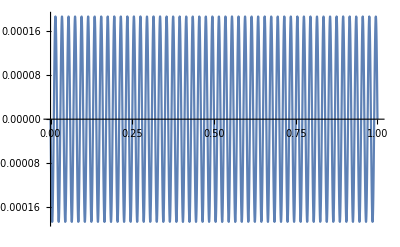

```mathematica
Plot[isolve/.{w->50*2Pi,U0->8,R1->2500,R2->2500,R3->4000,Rx->3000,r->100,C[1]->0,c->1},{t,0,1}]
```

```mathematica
isolve/.{w->50,U0->8,R1->2500,R2->2500,R3->4000,Rx->3000,r->100,C[1]->0,c->1}
```

{-(67 (5362500000000 Cos[50 t]-26750000 Sin[50 t]))/77103114259731101953125-(2 Sin[50 t])/10725}

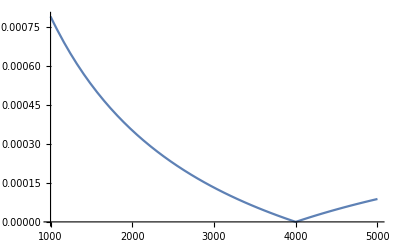

```mathematica
Plot[FindMaximum[isolve/.{w->50,U0->8,R1->2500,R2->2500,R3->4000,Rx->a,r->100,C[1]->0,c->1},{t,0}][[1]]/Sqrt[2],{a,1000,5000}]
```

```mathematica
FindRoot[FindMaximum[isolve/.{w->50,U0->8,R1->2500,R2->2500,Rx->R3*a,R3->b,r->100,C[1]->0,c->1},{t,0}][[1]]/Sqrt[2],
```

```mathematica
relation[r1_,r2_,r3_,rx_,R_,u0_,q_,omega_]:=FindMaximum[isolve/.{w->omega,U0->u0,R1->r1,R2->r2,R3->r3,Rx->rx,r->R,C[1]->0,c->q},{t,0}][[1]]/Sqrt[2];
```

```mathematica
Plot[relation[
```

```mathematica
FindRoot[relation[2500,2500,2500,x,100,8,1,50],{x,2500}]
```

FindMaximum::nrnum: The function value 0.+(1300000000000000 («1»)^2 («1»)^3 (0.+50. (12500000 x+6750000 (2500+x))))/((16894250000+19250000 x) («1»)^3 («1»)^2 («1») (12500000 (ⅈ+50 x)+6750000 (ⅈ+50 Plus[«2»]))) is not a real number at {t} = {0.}.

FindRoot::nlnum: The function value {0.707107 (0.-(1.89349×10^-21+1.37933×10^-42 ⅈ) (3.25×10^12 Cos[Times[«2»]]-1.925×10^7 Sin[Times[«2»]]))} is not a list of numbers with dimensions {1} at {x} = {2500.}.

FindRoot[relation[2500,2500,2500,x,100,8,1,50],{x,2500}]

```mathematica
ReleaseHold[Hold[relation[2500,2500,2500,x,100,8,1,50]]/.x->4000]
```

0.000225973

```mathematica
findroot[body_,target_,stepsize_,initialstep_,max_]:=Module[
{step,result},
step=initialstep;
result={While[ReleaseHold[body/.target->step]<max,step-=initialstep],While[ReleaseHold[Hold[body]/.target->step]<max,step+=initialstep]};
result
];
```

```mathematica
findroot[Hold[relation[2500,2500,2500,x,100,8,1,50]],x,1,4000,1*10^(-6)]
```

```mathematica
testlist=Table[Table[{2500,2500+100 a,(2500+100 a)/2500*1000+b,1000,100,8,q,50},{a,-10,20},{b,-100,100,0.2}],{q,0.1,1,0.1}]
```

{1}
 |  |  |  |

```mathematica
testlist[[1,1]]//Length
```

1001

```mathematica
relation@@@Flatten[testlist,2]
```

{0.000171941,0.000171563,0.000171185,310304,0.0000293771,0.0000294338,0.0000294904}
 |  |  |  |

```mathematica
simulationdata=%110;
```

```mathematica
ratiosentivitymatrix=Table[Transpose[{Table[2500/(2500+100a),{a,-10,20}],(Partition[Length/@(Select[#,#<q*10^-6&]&/@Partition[simulationdata,1001]),31][[1]]/10/1000)*Table[2500/(2500+100a),{a,-10,20}]}],{q,1,100,5}];
```

```mathematica
Export["R1R2Ratio.eps",GraphFormatize@ListLinePlot[ratiosentivitymatrix,PlotStyle->Table[{Opacity[0.2+a/200],RGBColor[1-a/100,0,a/100-0.1]},{a,1,100,5}],FrameLabel->MaTeX/@{"R_1/R_2","RD"}]]
```

R1R2Ratio.eps

```mathematica
Partition[Partition[Partition[simulationdata,201],31],10][[1,1]]
```

```mathematica
relation[2500,2500,2500,x,100,8,1,50]
Table[{While[ReleaseHold[body/.target->step]<max,step-=initialstep],While[ReleaseHold[Hold[body]/.target->step]<max,step+=initialstep]}
```

{Null,Null}

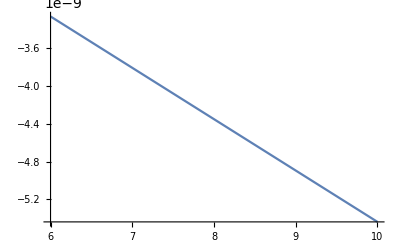

```mathematica
Plot[relation[2500,2500,2500,2500,100,x,1,50],{x,6,10}]
```

```mathematica
testlist2=Table[Table[{2500,2500+100 a,(2500+100 a)/2500*1000+b,1000,100,8,q/10^10,50},{a,-10,20},{b,-100,100,0.2}],{q,0.1,1,0.2}]
```

{{{{2500,1500,500.,1000,100,8,1.×10^-11,50},999,{2500,1500,700.,1000,100,8,1.×10^-11,50}},29,{1}},3,{1}}
 |  |  |  |

```mathematica
simulationdata2=relation@@@Flatten[testlist2,2]
```

{0.00137972,0.00137954,0.00137936,0.00137918,155148,0.00100826,0.00100821,0.00100815}
 |  |  |  |

```mathematica
ratiosentivitymatrix2=Table[Table[Transpose[{Table[2500/(2500+100a),{a,-10,20}],(Partition[Length/@(Select[#,#<q*10^-6&]&/@Partition[simulationdata,1001]),31][[k]]/10/1000)*Table[2500/(2500+100a),{a,-10,20}]}],{q,1,100,5}],{k,1,5}];
```

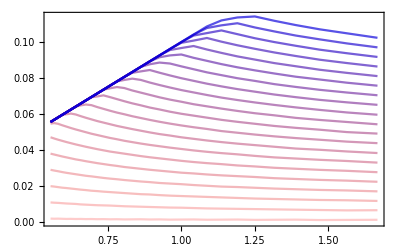

```mathematica
GraphFormatize@ListLinePlot[ratiosentivitymatrix2[[1]],PlotStyle->Table[{Opacity[0.2+a/200],RGBColor[1-a/100,0,a/100-0.1]},{a,1,100,5}],FrameLabel->MaTeX/@{"R_1/R_2","RD/\%"}]
```

```mathematica
Partition[Partition[simulationdata,1001],31][[All,10,10]]
```

{0.0000851692,0.0000851691,0.000085169,0.000085169,0.000085169,0.000085169,0.000085169,0.000085169,0.000085169,0.000085169}

```mathematica
Partition[Partition[simulationdata2,1001],31][[All,10,4]]
```

{0.001268,0.001268,0.001268,0.001268,0.001268}

```mathematica
testlist3=Table[Table[{2500,2500,1000+b,1000,100,8,10^(-q),50},{b,-100,100,0.2}],{q,0,10,0.2}]
```

{{{2500,2500,900.,1000,100,8,1.,50},{2500,2500,900.2,1000,100,8,1.,50},997,{2500,2500,1099.8,1000,100,8,1.,50},{2500,2500,1100.,1000,100,8,1.,50}},49,{1}}
 |  |  |  |

```mathematica
simulationdata3=relation@@@Flatten[testlist3,1]
```

{0.0000816285,0.0000814542,0.0000812799,0.0000811057,51044,0.00115465,0.00115455,0.00115446}
 |  |  |  |

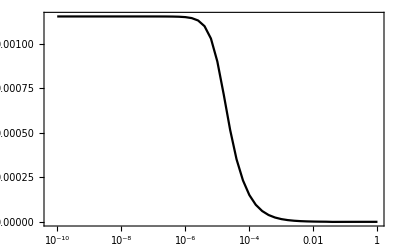

Ci.png

```mathematica
GraphFormatize[ListLinePlot[Transpose[{Table[10^-q,{q,0,10,0.2}],Flatten[MapThread[Extract,{Partition[simulationdata3,1001],Flatten[(Position[#,1]&/@MinDetect/@Partition[simulationdata3,1001]),1]}]]}],ScalingFunctions->{"Log",None},PlotRange->All,PlotStyle->Black,FrameLabel->MaTeX/@{"C/F","i/\mathrm{A}"}]]
Export["Ci.png",%,ImageResolution->500]
```

```mathematica
Position[#,1]&/@MinDetect/@Partition[simulationdata3,1001]
```

{{{501}},{{501}},{{501}},{{501}},{{501}},{{501}},{{501}},{{501}},{{501}},{{501}},{{501}},{{501}},{{501}},{{501}},{{502}},{{502}},{{504}},{{509}},{{521}},{{551}},{{627}},{{816}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}},{{1001}}}

```mathematica
Export["ideltaRcurve.eps",GraphFormatize[ListLinePlot[Partition[Transpose[{Flatten@Table[Table[1/1000 a,{a,-100,100,0.2}],51],simulationdata3}],1001][[14;;23]],PlotStyle->Table[{Opacity[a/10+0.1],RGBColor[1-a/10,0,a/10]},{a,10}],PlotLegends->MaTeX/@Table["10^{-"<>ToString@(0.2i)<>"}",{i,14,23}],AspectRatio->1,FrameLabel->MaTeX/@{"\Delta R","i/\mathrm{A}"}]]]
```

OptionValue::nodef: Unknown option PlotStyle for Graphics.

ideltaRcurve.eps

```mathematica
Partition[simulationdata3,1001]//Length
```

51

```mathematica
Flatten[(Position[#,1]&/@MinDetect/@Partition[simulationdata3,1001]),1]
```

{{501},{501},{501},{501},{501},{501},{501},{501},{501},{501},{501},{501},{501},{501},{502},{502},{504},{509},{521},{551},{627},{816},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001},{1001}}

```mathematica
Table[1/1000 a,{a,-100,100,0.2}]
```

{-0.1,-0.0998,-0.0996,-0.0994,-0.0992,-0.099,-0.0988,-0.0986,-0.0984,-0.0982,-0.098,-0.0978,-0.0976,-0.0974,-0.0972,-0.097,-0.0968,-0.0966,-0.0964,-0.0962,-0.096,-0.0958,-0.0956,-0.0954,-0.0952,-0.095,-0.0948,-0.0946,-0.0944,-0.0942,-0.094,-0.0938,-0.0936,-0.0934,-0.0932,-0.093,-0.0928,-0.0926,-0.0924,-0.0922,-0.092,-0.0918,-0.0916,-0.0914,-0.0912,-0.091,-0.0908,-0.0906,-0.0904,-0.0902,-0.09,-0.0898,-0.0896,-0.0894,-0.0892,-0.089,-0.0888,-0.0886,-0.0884,-0.0882,-0.088,-0.0878,-0.0876,-0.0874,-0.0872,-0.087,-0.0868,-0.0866,-0.0864,-0.0862,-0.086,-0.0858,-0.0856,-0.0854,-0.0852,-0.085,-0.0848,-0.0846,-0.0844,-0.0842,-0.084,-0.0838,-0.0836,-0.0834,-0.0832,-0.083,-0.0828,-0.0826,-0.0824,-0.0822,-0.082,-0.0818,-0.0816,-0.0814,-0.0812,-0.081,-0.0808,-0.0806,-0.0804,-0.0802,-0.08,-0.0798,-0.0796,-0.0794,-0.0792,-0.079,-0.0788,-0.0786,-0.0784,-0.0782,-0.078,-0.0778,-0.0776,-0.0774,-0.0772,-0.077,-0.0768,-0.0766,-0.0764,-0.0762,-0.076,-0.0758,-0.0756,-0.0754,-0.0752,-0.075,-0.0748,-0.0746,-0.0744,-0.0742,-0.074,-0.0738,-0.0736,-0.0734,-0.0732,-0.073,-0.0728,-0.0726,-0.0724,-0.0722,-0.072,-0.0718,-0.0716,-0.0714,-0.0712,-0.071,-0.0708,-0.0706,-0.0704,-0.0702,-0.07,-0.0698,-0.0696,-0.0694,-0.0692,-0.069,-0.0688,-0.0686,-0.0684,-0.0682,-0.068,-0.0678,-0.0676,-0.0674,-0.0672,-0.067,-0.0668,-0.0666,-0.0664,-0.0662,-0.066,-0.0658,-0.0656,-0.0654,-0.0652,-0.065,-0.0648,-0.0646,-0.0644,-0.0642,-0.064,-0.0638,-0.0636,-0.0634,-0.0632,-0.063,-0.0628,-0.0626,-0.0624,-0.0622,-0.062,-0.0618,-0.0616,-0.0614,-0.0612,-0.061,-0.0608,-0.0606,-0.0604,-0.0602,-0.06,-0.0598,-0.0596,-0.0594,-0.0592,-0.059,-0.0588,-0.0586,-0.0584,-0.0582,-0.058,-0.0578,-0.0576,-0.0574,-0.0572,-0.057,-0.0568,-0.0566,-0.0564,-0.0562,-0.056,-0.0558,-0.0556,-0.0554,-0.0552,-0.055,-0.0548,-0.0546,-0.0544,-0.0542,-0.054,-0.0538,-0.0536,-0.0534,-0.0532,-0.053,-0.0528,-0.0526,-0.0524,-0.0522,-0.052,-0.0518,-0.0516,-0.0514,-0.0512,-0.051,-0.0508,-0.0506,-0.0504,-0.0502,-0.05,-0.0498,-0.0496,-0.0494,-0.0492,-0.049,-0.0488,-0.0486,-0.0484,-0.0482,-0.048,-0.0478,-0.0476,-0.0474,-0.0472,-0.047,-0.0468,-0.0466,-0.0464,-0.0462,-0.046,-0.0458,-0.0456,-0.0454,-0.0452,-0.045,-0.0448,-0.0446,-0.0444,-0.0442,-0.044,-0.0438,-0.0436,-0.0434,-0.0432,-0.043,-0.0428,-0.0426,-0.0424,-0.0422,-0.042,-0.0418,-0.0416,-0.0414,-0.0412,-0.041,-0.0408,-0.0406,-0.0404,-0.0402,-0.04,-0.0398,-0.0396,-0.0394,-0.0392,-0.039,-0.0388,-0.0386,-0.0384,-0.0382,-0.038,-0.0378,-0.0376,-0.0374,-0.0372,-0.037,-0.0368,-0.0366,-0.0364,-0.0362,-0.036,-0.0358,-0.0356,-0.0354,-0.0352,-0.035,-0.0348,-0.0346,-0.0344,-0.0342,-0.034,-0.0338,-0.0336,-0.0334,-0.0332,-0.033,-0.0328,-0.0326,-0.0324,-0.0322,-0.032,-0.0318,-0.0316,-0.0314,-0.0312,-0.031,-0.0308,-0.0306,-0.0304,-0.0302,-0.03,-0.0298,-0.0296,-0.0294,-0.0292,-0.029,-0.0288,-0.0286,-0.0284,-0.0282,-0.028,-0.0278,-0.0276,-0.0274,-0.0272,-0.027,-0.0268,-0.0266,-0.0264,-0.0262,-0.026,-0.0258,-0.0256,-0.0254,-0.0252,-0.025,-0.0248,-0.0246,-0.0244,-0.0242,-0.024,-0.0238,-0.0236,-0.0234,-0.0232,-0.023,-0.0228,-0.0226,-0.0224,-0.0222,-0.022,-0.0218,-0.0216,-0.0214,-0.0212,-0.021,-0.0208,-0.0206,-0.0204,-0.0202,-0.02,-0.0198,-0.0196,-0.0194,-0.0192,-0.019,-0.0188,-0.0186,-0.0184,-0.0182,-0.018,-0.0178,-0.0176,-0.0174,-0.0172,-0.017,-0.0168,-0.0166,-0.0164,-0.0162,-0.016,-0.0158,-0.0156,-0.0154,-0.0152,-0.015,-0.0148,-0.0146,-0.0144,-0.0142,-0.014,-0.0138,-0.0136,-0.0134,-0.0132,-0.013,-0.0128,-0.0126,-0.0124,-0.0122,-0.012,-0.0118,-0.0116,-0.0114,-0.0112,-0.011,-0.0108,-0.0106,-0.0104,-0.0102,-0.01,-0.0098,-0.0096,-0.0094,-0.0092,-0.009,-0.0088,-0.0086,-0.0084,-0.0082,-0.008,-0.0078,-0.0076,-0.0074,-0.0072,-0.007,-0.0068,-0.0066,-0.0064,-0.0062,-0.006,-0.0058,-0.0056,-0.0054,-0.0052,-0.005,-0.0048,-0.0046,-0.0044,-0.0042,-0.004,-0.0038,-0.0036,-0.0034,-0.0032,-0.003,-0.0028,-0.0026,-0.0024,-0.0022,-0.002,-0.0018,-0.0016,-0.0014,-0.0012,-0.001,-0.0008,-0.0006,-0.0004,-0.0002,0.,0.0002,0.0004,0.0006,0.0008,0.001,0.0012,0.0014,0.0016,0.0018,0.002,0.0022,0.0024,0.0026,0.0028,0.003,0.0032,0.0034,0.0036,0.0038,0.004,0.0042,0.0044,0.0046,0.0048,0.005,0.0052,0.0054,0.0056,0.0058,0.006,0.0062,0.0064,0.0066,0.0068,0.007,0.0072,0.0074,0.0076,0.0078,0.008,0.0082,0.0084,0.0086,0.0088,0.009,0.0092,0.0094,0.0096,0.0098,0.01,0.0102,0.0104,0.0106,0.0108,0.011,0.0112,0.0114,0.0116,0.0118,0.012,0.0122,0.0124,0.0126,0.0128,0.013,0.0132,0.0134,0.0136,0.0138,0.014,0.0142,0.0144,0.0146,0.0148,0.015,0.0152,0.0154,0.0156,0.0158,0.016,0.0162,0.0164,0.0166,0.0168,0.017,0.0172,0.0174,0.0176,0.0178,0.018,0.0182,0.0184,0.0186,0.0188,0.019,0.0192,0.0194,0.0196,0.0198,0.02,0.0202,0.0204,0.0206,0.0208,0.021,0.0212,0.0214,0.0216,0.0218,0.022,0.0222,0.0224,0.0226,0.0228,0.023,0.0232,0.0234,0.0236,0.0238,0.024,0.0242,0.0244,0.0246,0.0248,0.025,0.0252,0.0254,0.0256,0.0258,0.026,0.0262,0.0264,0.0266,0.0268,0.027,0.0272,0.0274,0.0276,0.0278,0.028,0.0282,0.0284,0.0286,0.0288,0.029,0.0292,0.0294,0.0296,0.0298,0.03,0.0302,0.0304,0.0306,0.0308,0.031,0.0312,0.0314,0.0316,0.0318,0.032,0.0322,0.0324,0.0326,0.0328,0.033,0.0332,0.0334,0.0336,0.0338,0.034,0.0342,0.0344,0.0346,0.0348,0.035,0.0352,0.0354,0.0356,0.0358,0.036,0.0362,0.0364,0.0366,0.0368,0.037,0.0372,0.0374,0.0376,0.0378,0.038,0.0382,0.0384,0.0386,0.0388,0.039,0.0392,0.0394,0.0396,0.0398,0.04,0.0402,0.0404,0.0406,0.0408,0.041,0.0412,0.0414,0.0416,0.0418,0.042,0.0422,0.0424,0.0426,0.0428,0.043,0.0432,0.0434,0.0436,0.0438,0.044,0.0442,0.0444,0.0446,0.0448,0.045,0.0452,0.0454,0.0456,0.0458,0.046,0.0462,0.0464,0.0466,0.0468,0.047,0.0472,0.0474,0.0476,0.0478,0.048,0.0482,0.0484,0.0486,0.0488,0.049,0.0492,0.0494,0.0496,0.0498,0.05,0.0502,0.0504,0.0506,0.0508,0.051,0.0512,0.0514,0.0516,0.0518,0.052,0.0522,0.0524,0.0526,0.0528,0.053,0.0532,0.0534,0.0536,0.0538,0.054,0.0542,0.0544,0.0546,0.0548,0.055,0.0552,0.0554,0.0556,0.0558,0.056,0.0562,0.0564,0.0566,0.0568,0.057,0.0572,0.0574,0.0576,0.0578,0.058,0.0582,0.0584,0.0586,0.0588,0.059,0.0592,0.0594,0.0596,0.0598,0.06,0.0602,0.0604,0.0606,0.0608,0.061,0.0612,0.0614,0.0616,0.0618,0.062,0.0622,0.0624,0.0626,0.0628,0.063,0.0632,0.0634,0.0636,0.0638,0.064,0.0642,0.0644,0.0646,0.0648,0.065,0.0652,0.0654,0.0656,0.0658,0.066,0.0662,0.0664,0.0666,0.0668,0.067,0.0672,0.0674,0.0676,0.0678,0.068,0.0682,0.0684,0.0686,0.0688,0.069,0.0692,0.0694,0.0696,0.0698,0.07,0.0702,0.0704,0.0706,0.0708,0.071,0.0712,0.0714,0.0716,0.0718,0.072,0.0722,0.0724,0.0726,0.0728,0.073,0.0732,0.0734,0.0736,0.0738,0.074,0.0742,0.0744,0.0746,0.0748,0.075,0.0752,0.0754,0.0756,0.0758,0.076,0.0762,0.0764,0.0766,0.0768,0.077,0.0772,0.0774,0.0776,0.0778,0.078,0.0782,0.0784,0.0786,0.0788,0.079,0.0792,0.0794,0.0796,0.0798,0.08,0.0802,0.0804,0.0806,0.0808,0.081,0.0812,0.0814,0.0816,0.0818,0.082,0.0822,0.0824,0.0826,0.0828,0.083,0.0832,0.0834,0.0836,0.0838,0.084,0.0842,0.0844,0.0846,0.0848,0.085,0.0852,0.0854,0.0856,0.0858,0.086,0.0862,0.0864,0.0866,0.0868,0.087,0.0872,0.0874,0.0876,0.0878,0.088,0.0882,0.0884,0.0886,0.0888,0.089,0.0892,0.0894,0.0896,0.0898,0.09,0.0902,0.0904,0.0906,0.0908,0.091,0.0912,0.0914,0.0916,0.0918,0.092,0.0922,0.0924,0.0926,0.0928,0.093,0.0932,0.0934,0.0936,0.0938,0.094,0.0942,0.0944,0.0946,0.0948,0.095,0.0952,0.0954,0.0956,0.0958,0.096,0.0962,0.0964,0.0966,0.0968,0.097,0.0972,0.0974,0.0976,0.0978,0.098,0.0982,0.0984,0.0986,0.0988,0.099,0.0992,0.0994,0.0996,0.0998,0.1}